## E = E ẑ, B = B ẑ

```mathematica
em=υ(B e kz vf χ)/(kx^2+ky^2+kz^2);
FullSimplify[Grad[em,{kx,ky,kz}]/.{kx->k Cos[ϕ] Sin[θ],ky->k Sin[θ] Sin[ϕ],kz->k Cos[θ]}]
```

{-(B e vf υ χ Cos[ϕ] Sin[2 θ])/k^2,-(B e vf υ χ Sin[2 θ] Sin[ϕ])/k^2,-(B e vf υ χ Cos[2 θ])/k^2}

```mathematica
Clear[B,kx,ky,kz,s,cq,vf,k,v0,vm,v0dotΩ,vmdotΩ,enm,det];
ass=Assumptions->{cq,vf, Ef,μ}∈ Reals && vf>0 && cq>0 && Ef>0 && μ>0;
krep={k->(√ϵ)/(√cq √vf)};
Be={0,0,B};
BdotΩ=0;
v0=2 cq k vf{Cos[ϕ] Sin[θ], Sin[θ] Sin[ϕ],Cos[θ]};
enm=υ(B e Cos[θ] vf χ)/k;
vm={-(B e vf υ χ Cos[ϕ] Sin[2 θ])/k^2,-(B e vf υ χ Sin[2 θ] Sin[ϕ])/k^2,-(B e vf υ χ Cos[2 θ])/k^2};
v0dotΩ=0;
vmdotΩ=0;det=(k^2 Sin[θ])/(2 √cq √vf √ϵ);
```

## flat band

```mathematica
(* zz comp, along with the Drude term:
-Graphics-;
only I1 survives:
-Graphics-*)Clear[cond0,cond1,c0,c1, δ, δp, δpp,cc1,cc2,cc3,cc4,cc5];Print["indep of B terms"];(* v03^2 δ[ϵminμ] *)
c0=v0[[3]] v0[[3]] δ;
cond0=e^2 τ Integrate[det c0 ,{θ,0,π}]//FullSimplify
Print["B-dep terms"];
c1=Simplify[(2v0[[3]] vm[[3]]) δ + enm (v0[[3]])^2  δp +2enm v0[[3]] vm[[3]] δp+(vm[[3]])^2 δ +(enm^2 v0[[3]] v0[[3]])/2 δpp  ]/.{υ^2->1,χ^2->1};
cond1=e^2 τ FullSimplify[Integrate[det c1,{θ,0,π}]]/.{υ^2->1,χ^2->1}
```

indep of B terms

(4 cq^(3/2) e^2 k^4 vf^(3/2) δ τ)/(3 √ϵ)

B-dep terms

(B^2 e^4 vf^(3/2) (7 δ+2 cq k^2 vf (-2 δp+3 cq k^2 vf δpp)) τ)/(15 √cq k^2 √ϵ)

```mathematica
fac=(B^2 e^4 vf^(3/2) τ)/(15 √cq  √ϵ);
cc1=SeriesCoefficient[cond1/fac,{δ,0,1},{δp,0,0},{δpp,0,0}]
cc2=SeriesCoefficient[cond1/fac,{δ,0,0},{δp,0,1},{δpp,0,0}]
cc3=SeriesCoefficient[cond1/fac,{δ,0,0},{δp,0,0},{δpp,0,1}]
cc1 δ+cc2 δp+cc3 δpp==cond1/fac//FullSimplify
```

7/k^2

-4 cq vf

6 cq^2 k^2 vf^2

True

```mathematica
Clear[int];
intdrude=FullSimplify[(4 cq^(3/2) e^2 k^4 vf^(3/2) τ)/(3 √ϵ) (* δ[ϵminμ] *)/.krep,Assumptions->ass]/.ϵ->μ
(* fprime'[ϵ] = ((∂fprime)/(∂k))/((∂ϵ)/(∂k)) = fprime'[k]/(2 cq k vf+s vf); fprime^(3)[ϵ] = ((∂fprime''[ϵ])/(∂k))/((∂ϵ)/(∂k)) = (-2 c fprime'[k]+(2 c k+s) fprime''[k])/((2 c k+s)^3 Subscript[v, F]^2) *)
int=fac FullSimplify[ cc1(*δ[ϵminμ]*)+D[- cc2((*fprime'[k]*)1)/(2 cq k vf),k](* δp[ϵminμ] *)+D[-cc3(-2 cq(* fprime'[k]*))/((2 cq k)^3 vf^2)(*δpp[ϵminμ]*),k]+D[cc3((2 cq k) (*fprime''[k]*))/((2 cq k)^3 vf^2)(*δpp[ϵminμ]*),{k,2}]/.krep,Assumptions->ass]/.ϵ->μ
```

(4 e^2 μ^(3/2) τ)/(3 √cq √vf)

(7 B^2 √cq e^4 vf^(5/2) τ)/(30 μ^(3/2))

```mathematica
FullSimplify[(B^2 e^4 cq^(3/2) (τrat-1)τ vf^3 √(4 cq EF+vf) (vf+√(cq EF vf) (6+√(vf/(4 cq EF+vf)))))/(36 EF π^2 (2 EF (cq vf)^(3/2)+cq vf^(3/2)√EF √(4 cq EF+vf)+vf^(3/2)√cq (vf-√(vf (4 cq EF+vf))))),ass]
```

(B^2 cq e^4 vf^2 √(4 cq EF+vf) (vf+√(cq EF vf) (6+√(vf/(4 cq EF+vf)))) τ (-1+τrat))/(36 EF π^2 (2 cq EF √vf+vf^(3/2)-vf √(4 cq EF+vf)+√(cq EF vf) √(4 cq EF+vf)))

```mathematica
rep={cq->c,vf->Subscript[v, F],EF->μ,τrat->Subscript[τ, G]/τ};
TeXForm[(B^2 cq e^4 vf^2 √(4 cq EF+vf)  τ (-1+τrat))/(36 EF π^2 (2 cq EF √vf+vf^(3/2)-vf √(4 cq EF+vf)+√(cq EF vf) √(4 cq EF+vf)))/.rep]
```

## Plots

{0.139653 τ,9.0516×10^-8 τ,2.2629×10^-6 τ}

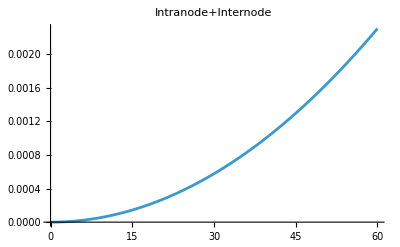

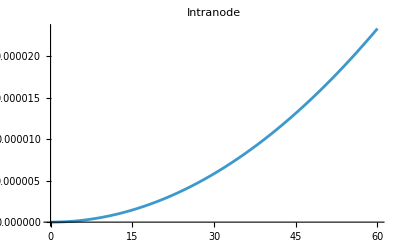

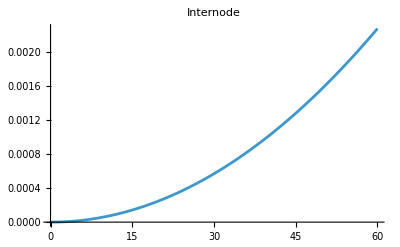

```mathematica
Clear[fn,finter,drude,x];
e=1;
drude[μ_,vf_,cq_]=1/(2π)^3(4 e^2 μ^(3/2) τ)/(3 √(cq vf));
fn[B_,μ_,vf_,cq_]=1/(2π)^3(7 B^2 √cq e^4 vf^(5/2) τ)/(30 μ^(3/2));
finter[B_,EF_,vf_,cq_,τrat_]=(B^2 e^4 cq^(3/2) (τrat-1)τ vf^3 √(4 cq EF+vf) (vf+√(cq EF vf) (6+√(vf/(4 cq EF+vf)))))/(36 EF π^2 (2 EF (cq vf)^(3/2)+cq vf^(3/2)√EF √(4 cq EF+vf)+vf^(3/2)√cq (vf-√(vf (4 cq EF+vf)))));

(*mu=0.1;cqval=0.1;vfval=0.005;trat=10 ;
x=drude[mu,vfval,cqval];
{x,fn[10,mu,vfval,cqval],fn[50,mu,vfval,cqval]}
Plot[{(fn[B,mu,vfval,cqval]+finter[B,mu,vfval,cqval,trat])/x},{B,0,60},PlotLabel->"Intranode+Internode"]
Plot[fn[B,mu,vfval,cqval]/x,{B,0,60},PlotLabel->"Intranode",PlotRange->All]
Plot[finter[B,mu,vfval,cqval,trat]/x,{B,0,60},PlotLabel->"Internode"]
*)
mu=0.1;lmu=0.05;cqval=0.001;vfval=0.005;trat=10 ;
x=drude[mu+lmu,vfval,cqval];
{x,fn[10,mu+lmu,vfval,cqval],fn[50,mu+lmu,vfval,cqval]}
Plot[{(fn[B,mu+lmu,vfval,cqval]+finter[B,mu,vfval,cqval,trat])/x},{B,0,60},PlotLabel->"Intranode+Internode"]
Plot[fn[B,mu+lmu,vfval,cqval]/x,{B,0,60},PlotLabel->"Intranode",PlotRange->All]
Plot[finter[B,mu,vfval,cqval,trat]/x,{B,0,60},PlotLabel->"Internode"]
Clear[e];
```

## without expanding OMM part in f

```mathematica
(* -Graphics-;
here Ω=0 and D=1 *)
w=v0+vm
entot=cq k k +enm;
int=w[[3]] w[[3]] δ[entot-μ]/.{υ ->1}
```

{2 cq k vf Cos[ϕ] Sin[θ]-(B e vf υ χ Cos[ϕ] Sin[2 θ])/k^2,2 cq k vf Sin[θ] Sin[ϕ]-(B e vf υ χ Sin[2 θ] Sin[ϕ])/k^2,2 cq k vf Cos[θ]-(B e vf υ χ Cos[2 θ])/k^2}

(2 cq k vf Cos[θ]-(B e vf χ Cos[2 θ])/k^2)^2 δ[cq k^2-μ+(B e vf χ Cos[θ])/k]

```mathematica
fn=cq k^2+χ(B e vf Cos[θ])/k;
sol=FullSimplify[Flatten[SolveValues[fn==μ,k],1][[1]],Assumptions->{cq,vf, Ef,μ,B,θ,e,χ}∈ Reals && vf>0 && cq>0 && Ef>0 && μ>0 && B>0 && e>0]/.χ^2->1
```

(2 3^(1/3) μ+2^(1/3) (-9 B √cq e vf χ Cos[θ]+√(-12 μ^3+81 B^2 cq e^2 vf^2 Cos[θ]^2))^(2/3))/(6^(2/3) (-9 B cq^2 e vf χ Cos[θ]+√3 √(cq^3 (-4 μ^3+27 B^2 cq e^2 vf^2 Cos[θ]^2)))^(1/3))

```mathematica
Clear[kf1,B,ifun];

kf1[μ_,vf_,cq_,B_,θ_,chi_]:=Block[{e=1},

1/(6 cq)(-2+((-8 vf^3-36 cq vf^2 μ-54 B chi cq^2 e vf^3 Cos[θ]+4 vf^(3/2) √(-4 (vf+3 cq μ)^3+vf (2 vf+9 cq μ+27/2 B chi cq^2 e vf Cos[θ])^2))^(1/3))/vf+(2 2^(2/3) (vf+3 cq μ))/(-18 cq vf^2 μ-vf^3 (4+27 B chi cq^2 e Cos[θ])+3 √3 cq √(vf^3) √(-4 μ^2 (vf+4 cq μ)+B chi e vf^2 Cos[θ] (8 vf+36 cq μ+27 B chi cq^2 e vf Cos[θ])))^(1/3))
];


ifun[μ_,vf_,cq_,B_,chi_]:=Block[{e=1,θ,kfvals,dat,len,i,list},
kfvals[θ_]=1/(6 cq)(-2+1/vf(-8 vf^3-36 cq vf^2 μ-54 B chi cq^2 e vf^3 Cos[θ]+4 vf^(3/2) √(-4 (vf+3 cq μ)^3+vf (2 vf+9 cq μ+27/2 B chi cq^2 e vf Cos[θ])^2))^(1/3)+(2 2^(2/3) (vf+3 cq μ))/(-18 cq vf^2 μ-vf^3 (4+27 B chi cq^2 e Cos[θ])+3 √3 cq √(vf^3) √(-4 μ^2 (vf+4 cq μ)+B chi e vf^2 Cos[θ] (8 vf+36 cq μ+27 B chi cq^2 e vf Cos[θ])))^(1/3));
dat=Table[{θ,kfvals[θ]//Chop},{θ,0,π,π/20}];
len=Length[dat];
list=Table[{dat[[i,1]]+dat[[len,1]]+π/20,dat[[len-i,2]] },{i,1,len-1}];
dat=Join[dat,list];
Interpolation[dat,PeriodicInterpolation->True]
];
mu=0.1;cqval=0.1;vfval=0.005;
ifun[mu,vfval,cqval,100,1]
```

InterpolatingFunction[…]

```mathematica
fn=cq k^2+χ(B e vf Cos[θ])/k;
D[fn,k]
```

2 cq k-(B e vf χ Cos[θ])/k^2

```mathematica
Clear[inti];
inti[χ_,B_,μ_,vf_,cq_]:=Block[{e=1,k,θ,fn,int},
k[θ_]=ifun[μ,vf,cq,B,χ][θ];
fn=cq k[θ]^2+χ(B e vf Cos[θ])/k[θ];
int[θ_]=k[θ]^2 Sin[θ](2 cq k[θ] vf Cos[θ]-χ(B e vf Cos[2 θ])/k[θ]^2)^2/Abs[2 cq k[θ]-(B e vf χ Cos[θ])/k[θ]^2];
NIntegrate[int[θ],{θ,0,π}]
];
mu=0.1;cqval=0.1;vfval=0.005;
inti[1,1,mu,vfval,cqval]
inti[-1,1,mu,vfval,cqval]
```

0.00333344

0.00333344

{{0,-1.11022×10^-16},{1,0.000033284},{2,0.000133138},{3,0.00029957},{4,0.000532589},{5,0.000832214},{6,0.00119846},{7,0.00163136},{8,0.00213095},{9,0.00269724},{10,0.0033303}}

{{0,-1.11022×10^-16},{1,0.000033284},{2,0.000133138},{3,0.00029957},{4,0.000532589},{5,0.000832214},{6,0.00119846},{7,0.00163136},{8,0.00213095},{9,0.00269724},{10,0.0033303}}

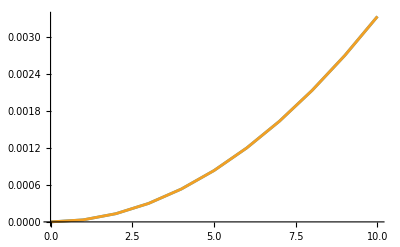

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;
chi=1;
x=inti[chi,0,mu,vfval,cqval];
dat1=Table[{B,inti[chi,B,mu,vfval,cqval]/x-1},{B, 0, 10,1}]
chi=-1;
x=inti[chi,0,mu,vfval,cqval];
dat2=Table[{B,inti[chi,B,mu,vfval,cqval]/x-1},{B, 0, 10,1}]
ListLinePlot[{dat1,dat2}]
```

```mathematica
(*-Graphics-; -Graphics-*)
```

```mathematica
Clear[sinter];
sinter[B_,μ_,vf_,cq_]:=Block[{e=1,dos1,dos2,k1,k2,θ,fn,χ,int1,int2,ρg},
χ=1;
k1[θ_]=ifun[μ,vf,cq,B,χ][θ];
dos1=NIntegrate[k1[θ]^2 Sin[θ]/Abs[2 cq k1[θ]-(B e vf χ Cos[θ])/k1[θ]^2],{θ,0,π}];

χ=-1;
k2[θ_]=ifun[μ,vf,cq,B,χ][θ];
dos2=NIntegrate[k2[θ]^2 Sin[θ]/Abs[2 cq k2[θ]-(B e vf χ Cos[θ])/k2[θ]^2],{θ,0,π}];
ρg=(dos1+dos2)/2;
int1=NIntegrate[k1[θ]^2 Sin[θ](2 cq vf Cos[θ] k1[θ]-(B e vf Cos[2 θ])/k1[θ]^2)/Abs[2 cq k1[θ]-(B e vf  Cos[θ])/k1[θ]^2],{θ,0,π}];
int2=NIntegrate[k2[θ]^2 Sin[θ](2 cq vf Cos[θ] k2[θ]+(B e vf Cos[2 θ])/k2[θ]^2)/Abs[2 cq k2[θ]+(B e vf  Cos[θ])/k2[θ]^2],{θ,0,π}];
{int1^2/ρg,int2^2/ρg}
];
mu=0.1;cqval=0.1;vfval=0.005;
sinter[10,mu,vfval,cqval]
```

{3.17379×10^-7,3.17379×10^-7}

```mathematica
vvec=2cq kf10[θ]vf{ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
vomm=(-χ  e B vf)/kf10[θ]^2{Cos[ϕ] Sin[2 θ], Sin[2 θ] Sin[ϕ], Cos[2 θ]};
(vvec+vomm)[[3]]
```

-(B e vf χ Cos[2 θ])/kf10[θ]^2+2 cq vf Cos[θ] kf10[θ]